```mathematica
(*Variables*)
g=1.5;
κ=.2;
L=10;
dx=.1;
numPoints=L/dx;
(*import statement for steady state solution.  you'll need to change this to wherever you save the steady state solution i send you*)
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa0p2G1p5_N50000"];
PhiVSYKappa0p2G1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa0p2G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])]
V[x_]:=2*Pi*κ*(1-Cos[2*Sqrt[Pi]*ϕss[x]]);
```

k = {0.+0.83106 ⅈ,0.595475,0.792202,1.21144,1.48457}

ω = {1.67809,1.965,2.03328,2.2303,2.38969}

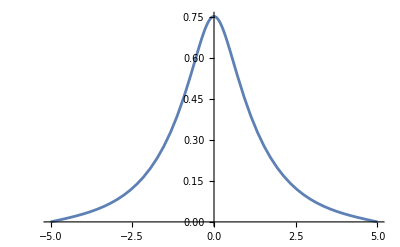

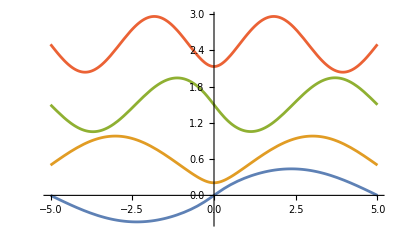

```mathematica
(*Calculating the first few eigenvalues using Dirichlet BCs as a test*)
total=5; (*total number of eigenvalues you feel like generating*)
intermediatePhi[x_]:=2*Sqrt[π]*ϕss[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x] +g^2;
(*DE solver*)
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->5000,"BasisSize"->total+1,"Shift"->3.2}];
Print["k = ",Sqrt[vals-g^2-2*Pi*κ]]
Print["ω = ",Sqrt[vals]]
Plot[fns[[1]],{x,-5,5},PlotRange->All]
Plot[{fns[[2]],fns[[3]]+.5,fns[[4]]+1.5,fns[[5]]+2.5},{x,-5,5}]
```

```mathematica
(*function which sets up and returns the finite difference matrix*)
FDmat[k_]:=Module[{laplacianMatrix,potentialmatrix,minus1λ,ϕsslist,cosphi},
laplacianMatrix=SparseArray[
{
{i_,j_}/;i==j->-2,
{i_,j_}/;Abs[i-j]==1->1
},
{numPoints-1,numPoints-1}]/dx^2;
laplacianMatrix[[1,1]]=-(1-I*k*dx)/dx^2;
laplacianMatrix[[numPoints-1,numPoints-1]]=-(1-I*k*dx)/dx^2;
ϕsslist=Table[{x,ϕss[x]},{x,-L/2+dx,L/2-dx,dx}];
cosphi=DiagonalMatrix[Cos[2*Sqrt[Pi]*ϕsslist[[All,2]]]];
potentialmatrix=2*Pi*κ*(IdentityMatrix[Round[numPoints-1]]-cosphi);
minus1λ=DiagonalMatrix[ConstantArray[k^2,Round[numPoints-1]]];
-laplacianMatrix-potentialmatrix-minus1λ
];
```

```mathematica
(*For a given k, computes the SVD and returns the lowest singular value and corresponding eigenvector*)
singval[kre_?NumericQ,kim_?NumericQ]:=Module[{k,testmat,σmin,U,Σ,Evecs,evec},
k=kre+I*kim;
testmat=FDmat[k];
σmin=Last@SingularValueList[testmat];
{U,Σ,Evecs}=SingularValueDecomposition[testmat];
evec=Evecs[[All,-1]];
<|"singval"->σmin,"evec"->evec|>
];
```

```mathematica
(*creates a matrix of the singular values as a function of the real and imaginary part of k*)
kimvals=Range[-1,2.5,.01];
krevals=Range[-.1,2,.01];
singvalslist=ConstantArray[-1,{Length[krevals],Length[kimvals]}];

For[i=1,i<=Length[krevals],i++,
For[j=1,j<=Length[kimvals],j++,
singvalslist[[i,j]]=singval[krevals[[i]],kimvals[[j]]]["singval"];
];
];
```

```mathematica
(*Plots said matrix as a function of the real and imaginary parts of k*)
ListDensityPlot[singvalslist,Mesh->None,InterpolationOrder->0,PlotLegends->Automatic,Frame->True,FrameLabel->{"Im[k]","Re[k]"},DataRange->{{-1,2.5},{-.1,2}}]
```

-Graphics-

```mathematica
minpos=Position[MinDetect[singvalslist],1](*this detects minima by checking that it is lower than all of the points around it in the array*)
Dimensions[singvalslist](*i spit out the dimensions here to check if i need to eliminate any minima that come from boundary values (not true minima)*)
minpos=minpos[[2;;-1]] (*This line eliminates a minimum that comes from a min along the boundary which is not actually a true local minimum if i were to sample more points*)
minpos=minpos[[1;;8]]
```

{{1,58},{11,16},{11,184},{36,59},{49,48},{91,63},{115,61},{152,67},{181,68},{211,71}}

{211,351}

{{11,16},{11,184},{36,59},{49,48},{91,63},{115,61},{152,67},{181,68},{211,71}}

{{11,16},{11,184},{36,59},{49,48},{91,63},{115,61},{152,67},{181,68}}

```mathematica
(*setting up things for plotting the eigenfunctions*)
remins=minpos[[All,1]];
immins=minpos[[All,2]];
xvals=Range[-L/2+dx,L/2-dx,dx];
```

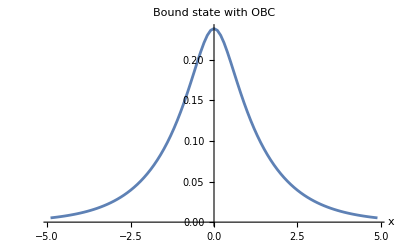

```mathematica
(*plot of the bound state*)
ListLinePlot[Transpose[{xvals,Re[singval[krevals[[remins[[2]]]],kimvals[[immins[[2]]]]]["evec"]]}],PlotRange->All,PlotLabel->"Bound state with OBC",AxesLabel->{"x"}]
```

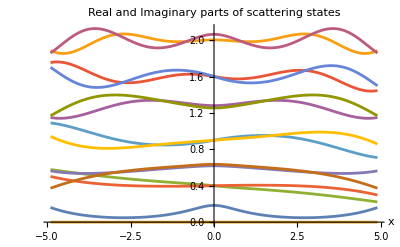

```mathematica
(*plot of the scattering states (both real and imaginary parts plotted together, i separate different mode n by translating them vertically upwards)*)
ListLinePlot[{Transpose[{xvals,Re[singval[krevals[[remins[[1]]]],kimvals[[immins[[1]]]]]["evec"]]}],Transpose[{xvals,Im[singval[krevals[[remins[[1]]]],kimvals[[immins[[1]]]]]["evec"]]}],Transpose[{xvals,Re[singval[krevals[[remins[[3]]]],kimvals[[immins[[3]]]]]["evec"]]+.4}],Transpose[{xvals,Im[singval[krevals[[remins[[3]]]],kimvals[[immins[[3]]]]]["evec"]]+.4}],Transpose[{xvals,Re[singval[krevals[[remins[[4]]]],kimvals[[immins[[4]]]]]["evec"]]+.6}],Transpose[{xvals,Im[singval[krevals[[remins[[4]]]],kimvals[[immins[[4]]]]]["evec"]]+.6}],Transpose[{xvals,Re[singval[krevals[[remins[[5]]]],kimvals[[immins[[5]]]]]["evec"]]+.9}],Transpose[{xvals,Im[singval[krevals[[remins[[5]]]],kimvals[[immins[[5]]]]]["evec"]]+.9}],Transpose[{xvals,Re[singval[krevals[[remins[[6]]]],kimvals[[immins[[6]]]]]["evec"]]+1.3}],Transpose[{xvals,Im[singval[krevals[[remins[[6]]]],kimvals[[immins[[6]]]]]["evec"]]+1.3}],Transpose[{xvals,Re[singval[krevals[[remins[[7]]]],kimvals[[immins[[7]]]]]["evec"]]+1.6}],Transpose[{xvals,Im[singval[krevals[[remins[[7]]]],kimvals[[immins[[7]]]]]["evec"]]+1.6}],Transpose[{xvals,Re[singval[krevals[[remins[[8]]]],kimvals[[immins[[8]]]]]["evec"]]+2}],Transpose[{xvals,Im[singval[krevals[[remins[[8]]]],kimvals[[immins[[8]]]]]["evec"]]+2}]},PlotRange->All,AxesLabel->{"x",""},PlotLabel->"Real and Imaginary parts of scattering states"]
```

0.00379156

{0.,0.,0.25,0.38,0.8,1.04,1.41,1.7}

{-0.85,0.83,-0.42,-0.53,-0.38,-0.4,-0.34,-0.33}

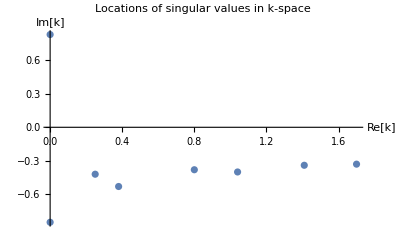

```mathematica
singval[krevals[[remins[[1]]]],kimvals[[immins[[1]]]]]["singval"]
singvalsre={krevals[[remins[[1]]]],krevals[[remins[[2]]]],krevals[[remins[[3]]]],krevals[[remins[[4]]]],krevals[[remins[[5]]]],krevals[[remins[[6]]]],krevals[[remins[[7]]]],krevals[[remins[[8]]]]}
singvalsim={kimvals[[immins[[1]]]],kimvals[[immins[[2]]]],kimvals[[immins[[3]]]],kimvals[[immins[[4]]]],kimvals[[immins[[5]]]],kimvals[[immins[[6]]]],kimvals[[immins[[7]]]],kimvals[[immins[[8]]]]}
ListPlot[Transpose[{singvalsre,singvalsim}],PlotRange->All,AxesLabel->{"Re[k]","Im[k]"},PlotLabel->"Locations of singular values in k-space"]
```

```mathematica
(*Plotting w*)
k1=singvalsre[[1]]+I*singvalsim[[1]];
ω1=Sqrt[k1^2+g^2+2*Pi*κ]
k2=singvalsre[[2]]+I*singvalsim[[2]];
ω2=Sqrt[k2^2+g^2+2*Pi*κ]
k3=singvalsre[[3]]+I*singvalsim[[3]];
ω3=Sqrt[k3^2+g^2+2*Pi*κ]
k4=singvalsre[[4]]+I*singvalsim[[4]];
ω4=Sqrt[k4^2+g^2+2*Pi*κ]
k5=singvalsre[[5]]+I*singvalsim[[5]];
ω5=Sqrt[k5^2+g^2+2*Pi*κ]
k6=singvalsre[[6]]+I*singvalsim[[6]];
ω6=Sqrt[k6^2+g^2+2*Pi*κ]
k7=singvalsre[[7]]+I*singvalsim[[7]];
ω7=Sqrt[k7^2+g^2+2*Pi*κ]
```

1.66857+0. ⅈ

1.67861+0. ⅈ

1.84282-0.0569779 ⅈ

1.83906-0.109513 ⅈ

2.00629-0.151524 ⅈ

2.11352-0.196828 ⅈ

2.32842-0.205891 ⅈ

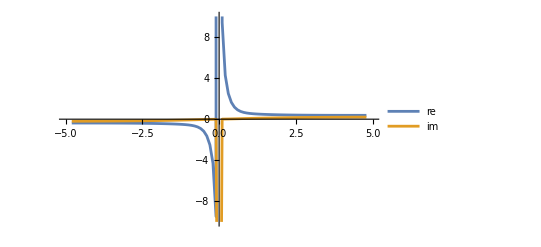

k= 0.21-0.38 ⅈ and ω= 2.90407-0.0274786 ⅈ

```mathematica
secondefun=singval[krevals[[remins[[2]]]],kimvals[[immins[[2]]]]]["evec"];
deriv=(secondefun[[3;;]]-secondefun[[;;-3]])/(2*dx);
secondresized=secondefun[[2;;-2]];
xvalsresized=xvals[[2;;-2]];
ListLinePlot[{Transpose[{xvalsresized,Re[deriv/secondresized]}],Transpose[{xvalsresized,Im[deriv/secondresized]}]},PlotRange->{{-5,5},{-10,10}},PlotLegends->{"re","im"}]
k=singvalsre[[2]]+I*singvalsim[[2]];
ω=Sqrt[k^2+g^2+2*Pi*κ];
Print["k= ",k," and ω= ",ω];
```